# Lab3 Овсейчук В.И., ПО-3

```mathematica
Упражнение 10.1а (Что следует вставить вместо Хааа чтобы получить график справа)
(*График аналитически заданной функции от xmin до xmax (логарифмическая шкала по обеим осям)*)
```

```mathematica
Row[{Plot[E^x,{x,1,5},ImageSize->270],
	LogLogPlot[E^x,{x,1,5},ImageSize->270]},Spacer[5]]
```

-Graphics--Graphics-

```mathematica
Упражнение 10.1b .
```

```mathematica
(*график кривой радиуса fPlt1 в зависимости от заданного угла в полярной системе координат*)
fPlt1 = {4/(2+Cos[t]), 4*Cos[t]-2};
g1=Plot[fPlt1, {t,0,2*Pi},ImageSize->260];
g2=PolarPlot[fPlt1, {t,0,2*Pi},ImageSize->260];
Row[{g1,g2},Spacer[15]]
```

-Graphics--Graphics-

```mathematica
Упражнение 10.1c
(*график кривой заданной параметрически*)
Row[{PolarPlot[Θ,{Θ,0,4*Pi},ImageSize->260], 
ParametricPlot[{Θ*Cos[Θ],Θ*Sin[Θ]},{Θ,0,4*Pi},ImageSize->260]},Spacer[15]]
```

-Graphics--Graphics-

```mathematica
Упражнение 10.2a . 
Генерирует график плотности распределения в процентах по наботу Хi
```

```mathematica
(*выводит график, на котором соединяются точки с координатам и значение-номер)*)
```

```mathematica
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
list3=Table[f3[x],{x,-5,5,0.4}];
grListLPl=ListLinePlot[list3,BaseStyle->16,
	GridLines->{{5,10,20,25},{-1,-0.5,0.5}},
	Mesh -> Full,Joined->True,
	AxesStyle->Directive[Black,Thick,14],
	Filling->Axis,FillingStyle->LightRed,
	AspectRatio->0.8,ImageSize->260];
grListPSP=ProbabilityScalePlot[list3,BaseStyle->16,
	Mesh -> Full,Joined->True,PlotStyle->Red,
	AxesStyle->Directive[Black,Thick,14],
	Filling->Axis,FillingStyle->LightCyan,
	AspectRatio->0.8,ImageSize->260];
Row[{grListLPl,grListPSP},Spacer[20]]
```

-Graphics--Graphics-

```mathematica
Упражнение 10.2b
(*график для сравнения совокупности данных с согласованным нормальным распределением*)
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
list3=Table[f3[x],{x,-5,5,0.4}];
grListLPl=ListLinePlot[list3,
	BaseStyle->16,Mesh -> Full,Joined->True,
	AxesStyle->Directive[Black,Thick,14],
	Filling->Axis,FillingStyle->LightRed,
	AspectRatio->0.8,ImageSize->260];
grListQP=QuantilePlot[list3,BaseStyle->16,
	Mesh -> Full,Joined->True,PlotStyle->Green,
	AxesStyle->Directive[Black,Thick,14],
	Filling->Axis,FillingStyle->LightCyan,
	AspectRatio->0.8,ImageSize->260];
Row[{grListLPl,grListQP},Spacer[20]]
```

-Graphics--Graphics-

```mathematica
Упражнение 10.2c
(*график плотности распределения случайной велечины*)
f3[x_]:=(-E^(-0.2*x^2))*Cos[5*x^2]-0.1*x
list3=Table[f3[x],{x,-5,5,0.4}];
grListLPl=ListLinePlot[list3,
	BaseStyle->16,Mesh -> Full,Joined->True,
	AxesStyle->Directive[Black,Thick,14],
	GridLines->{{5,10,20,25},{-1,-0.5,0.5}},
	GridLinesStyle->Directive[Gray,Dashed],
	
	Filling->Axis,FillingStyle->LightRed,
	AspectRatio->1.,ImageSize->260];

grListPP=ProbabilityPlot[list3,
	BaseStyle->16,Mesh -> Full,Joined->True,
	PlotStyle->Magenta,
	AxesStyle->Directive[Black,Thick,14],
	Filling->Axis,FillingStyle->LightCyan,
	AspectRatio->1.,ImageSize->260];
Row[{grListLPl,grListPP},Spacer[20]]
```

-Graphics--Graphics-

```mathematica
Упражнение 10.1d
(*вывод секторной диаграммы (сектора радиуса y и пропорциональные x)*)
lstCh1={2,4,8,4};
lstCh2={{2,4},{4,3},{8,2},{4,3}};
grCh1=PieChart[lstCh1,BaseStyle->16,ImageSize->250,
	ChartStyle->{Red,Magenta,Green,Blue},
	ChartLabels->Placed[lstCh1,"RadialOuter"]];

grCh2 = SectorChart[lstCh2,BaseStyle->16,ImageSize->320,
	ChartStyle->{Red,Magenta,Green,Blue},
	ChartLabels->Placed[lstCh2,"RadialOuter"]];
Row[{grCh1,grCh2}]
```

-Graphics--Graphics-

```mathematica
Упражнение 10.1e . 
(*ступенчатый график от календарного времени*)
```

```mathematica
fDataO={{{2016,11,17},63},{{2016,11,18},64.4},{{2016,11,21},65.0},{{2016,11,22},66.3},{{2016,11,23},65.9},{{2016,11,25},67.6},{{2016,11,28},66.6},{{2016,11,29},67.1},{{2016,11,30},67.5}};
grDLP=DateListPlot[fDataO,BaseStyle->14,ImageSize->260];
grDLSP=DateListStepPlot[fDataO,BaseStyle->14,ImageSize->260];
Row[{grDLP,grDLSP},Spacer[20]]
```

-Graphics--Graphics-

```mathematica
Упражнение 10.1f
```

```mathematica
(*генерация диаграммы, показывающие цены объёмы продаж на каждую дату диапазона*)
(*не работает чего-то InteractiveTradingChart*)
```

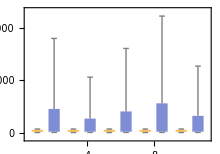
-Graphics--Graphics-

```mathematica
fdataOHLCV={{{2017,10,23},{65.9,68.,64.9,67.5,53950}},
{{2017,10,24},{67.6,67.8,66.3,66.9,31740}},
{{2017,10,25},{66.6,67.6,66.1,66.9,48200}},
{{2017,10,26},{67.1,68.1,66.5,67.5,66750}},
{{2017,10,27},{67.5,67.9,65.8,65.9,38080}}};

grTrCh=TradingChart[fdataOHLCV,AspectRatio->7/10,
	ImageSize->260,TrendStyle->{Blue,Magenta}];
grITrCh=InteractiveTradingChart[fdataOHLCV,AspectRatio->7/10,ImageSize->220];
Row[{grTrCh,grITrCh},Spacer[10]]
```

```mathematica
Упражнение 10.1g. 
(*диаграмма потока*)
```

```mathematica
grfCP1=ContourPlot[{Cos[x+y^2]*2y Cos[x+y^2]},{x,-2,2},{y,-2,2},Contours->10,BaseStyle->{12},ImageSize->250];
grStrPl1=StreamPlot[{Cos[x+y^2],2y Cos[x+y^2]},{x,-2,2},{y,-2,2},StreamStyle->Blue,BaseStyle->{12},ImageSize->250];
Row[{grfCP1,grStrPl1},Spacer[10]]
```

-Graphics--Graphics-

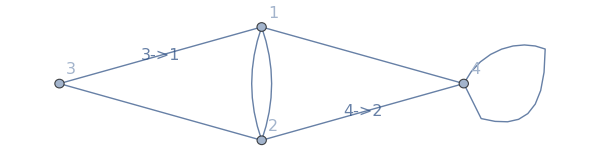

-Graphics-

```mathematica
Упражнение 10.1h . Изображение выражений в виде дерева с разными уровнями по глубинам(деревовидные графы)
(*генерирует графическое дерево графа на плоскости*)
fTrFrm={1->2,2->1,{3->1,"3->1"},
	3->2,4->1,{4->2,"4->2"},4->4};

GraphPlot[fTrFrm,VertexLabeling->True,
	BaseStyle->16,AspectRatio->3/10,ImageSize->600]

TreeForm[fTrFrm,DirectedEdges->True,BaseStyle->16,
	VertexLabeling->True,AspectRatio->3/10,
ImageSize->600]
```